```mathematica
w0 = 23.78*10^-4
```

0.002378

```mathematica
z0 = -7.2
```

-7.2

```mathematica
lente1 = 28(*distância da lente 1 até o espelho*)
f1 = 20
f2 = 12.5
lente2 = 58(*distância da lente 2 até o espelho*)
lambda = 780*10^-7
```

28

20

12.5

58

39/500000

```mathematica
v1 = {3*2.54,4*2.54,5*2.54,6*2.54,7*2.54,8*2.54,9*2.54}
v2 = {0.1225, 0.1324, 0.1530, 0.1715, 0.1880, 0.1997, 0.2122}
```

{7.62,10.16,12.7,15.24,17.78,20.32,22.86}

{0.1225,0.1324,0.153,0.1715,0.188,0.1997,0.2122}

```mathematica
q[z_]:=(1/((z-z0)(1+(((π w0^2)/λ)/(z-z0))^2))-ⅈ λ/(π (w0 √(1+((z-z0)/((π w0^2)/λ))^2))^2))^-1
```

```mathematica
w[z_]:=(-π/λ Im[1/q[z]])^(-1/2)
```

```mathematica
L[f_,z_]:=({{1, z}, {0, 1}}).({{1, 0}, {-1/f, 1}})
```

```mathematica
qL1[z_]:=(L[f1,z][[1,1]]q[lente1]+L[f1,z][[1,2]])/(L[f1,z][[2,1]]q[lente1]+L[f1,z][[2,2]])
```

```mathematica
wL1[z_]:=(-π/λ Im[1/qL1[z]])^(-1/2)
qL2[z_]:=(L[f2,z][[1,1]]q[lente2]+L[f2,z][[1,2]])/(L[f2,z][[2,1]]q[lente2]+L[f2,z][[2,2]])
wL2[z_]:=(-π/λ Im[1/qL2[z]])^(-1/2)
```

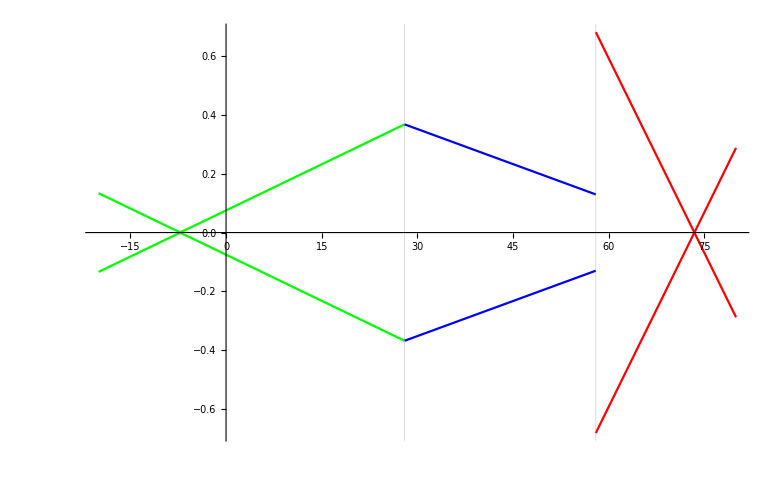

```mathematica
plot1 = Plot[
{w[z],-w[z]},
{z,-20,lente1},
PlotStyle->{Green,Green}
]; (*plot do feixe gaussiano ao sair da fibra*)
plot2=Plot[
{wL1[z-lente1],-wL1[z-lente1]},
{z,lente1,lente2},
PlotStyle->{Blue,Blue}
];(*plot do feixe gaussiano após passa pela lente 1*)

plot3 =Plot[
{wL2[z-lente2],-wL2[z-lente2]},
{z,lente2,80},
PlotStyle->{Red,Red}
];

Show[(*{plot1,plot2, ListPlot[data]}*)
{plot1,plot2, plot3},
GridLines->{{{lente1,{Blue,Dashed}},{lente2,{Red,Dashed}}},{}},
PlotRange->{{-20,80},All}]
```

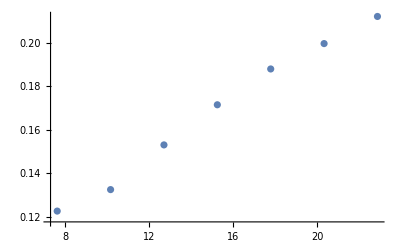

```mathematica
data=Transpose@{v1,v2};
ListPlot[data]
```

```mathematica
wL2[70.3-lente2]
```

0.00125536